# Dilo con Mathematica 2023

Luis Gerardo Ramirez Archundia

```mathematica
f[x_]:=Sqrt[1-(Abs[x]-1)^2];
g[x_]:=ArcCos[1-Abs[x]]-Pi;
Plot[{f[x],g[x]},{x,-2,2}, AspectRatio->Automatic, PlotTheme->"Marketing", Filling->Bottom]
```

-Graphics-

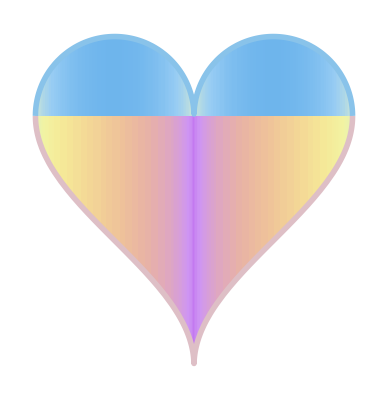

```mathematica
Plot[{f[x],g[x]},{x,-2,2}, AspectRatio->Automatic, PlotStyle->{{RGBColor[0.5,0.2,0.5], Thickness[0.01]},{RGBColor[0.5,0.2,0.5], Thickness[0.01]}}, Axes->False, Filling->Axis, ColorFunction->"Pastel"]
```

```mathematica
RegionPlot3D[((x^2+(9 y^2)/4+z^2-1)^3-x^2 z^3-(9 y^2 z^3)/80)<0, {x,-1.3,1.3},{y,-1.3,1.3},{z,-1.3,1.3}, PlotStyle->{Specularity[White,40]}, Mesh->{5,5}, Lighting->"ThreePoint", PlotPoints->50, ColorFunction->"NeonColors", Axes->False, Boxed->False]
```

-Graphics3D-